```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichiro/Documents/Univ/quantum_stochastic/math

```mathematica
Integrate[a Exp[(-(Np-Ns)^2)/(2 s^2)],{Np,0,NN}]//Simplify
```

a √(π/2) s (Erf[(NN-Ns)/(√2 s)]+Erf[Ns/(√2 s)])

```mathematica
f[x_]=a(Erf[(x-b)/c]+Erf[b/c]);
```

## Chaotic

```mathematica
mm=2.11 10^-2;
```

```mathematica
V[x_]=1/2 mm^2 x^2;
```

```mathematica
H[x_,p_]=Sqrt[(p^2/2+V[x])/3];
eH[x_,p_]=p^2/(2 H[x,p]^2);
```

```mathematica
xi=11;
pi=-Sqrt[2/3]mm;
Hi=H[xi,pi];
```

```mathematica
tf=100/Hi;
```

```mathematica
sol=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==xi,x'[0]==pi,NN'[t]==H[x[t],x'[t]],NN[0]==0},{x[t],x'[t],NN[t]},{t,0,tf}][[1]];
```

```mathematica
Nsol[t_]=NN[t]/.sol;
eHsol[t_]=eH[x[t],x'[t]]/.sol;
```

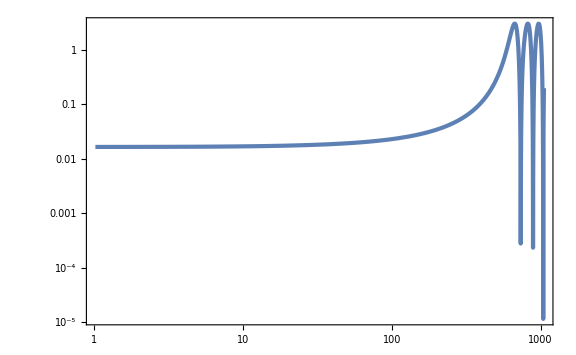

```mathematica
LogLogPlot[eHsol[t],{t,0,tf},PlotRange->Full]
```

```mathematica
tend=t/.FindRoot[eHsol[t]==1,{t,500}]
```

591.954

```mathematica
Nend=Nsol[tend]
```

30.6863

```mathematica
MS=Import["calPlin_chaotic.csv"];
```

```mathematica
calPvsNb=Map[{Nend-Log[#[[1]]],#[[2]]}&,MS];
```

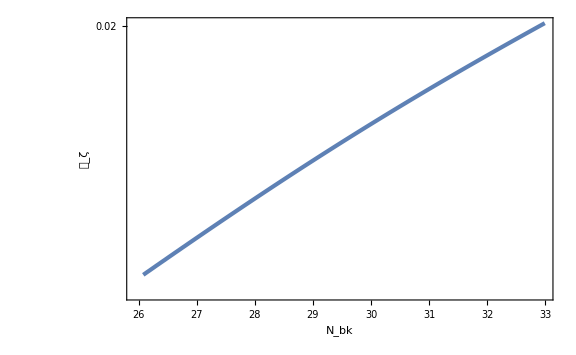

```mathematica
ListLogPlot[calPvsNb,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, "bk"],"Chaotic"}}]
```

```mathematica
MiyamotoData=Import["NTot_Chaotic_RandomNbk_1e7path.csv"];//AbsoluteTiming
```

{28.1674,Null}

#### 1e6

```mathematica
sample=10^6;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
Nbmin=Min[dN2vsNb[[All,1]]]
Nmax=Max[dN2vsNb[[All,1]]]
```

1.00001

25.

```mathematica
fit=NonlinearModelFit[dN2vsNb,f[x],{a,b,c},x]
```

b        -b + x
FittedModel[<|Type -> Nonlinear, Model -> <|FittedParameterRules -> {a -> 0.0923362, b -> 31.0445, c -> 16.4128}, IndependentVariables -> {x}, FitExpression -> a (Erf[-] + Erf[------]), ParameterConstraints -> True|>, Weights -> <|ExampleWeights -> 1|>, InputData -> {«1000000»}, Localizer -> Function[Null, Internal`LocalizedBlock[{a, b, c, x}, #1], {HoldAll}], Options -> {}|>]
                                                                                                                                                                       c          c

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.0923362 (0.992526+Erf[0.0609279 (-31.0445+x)])

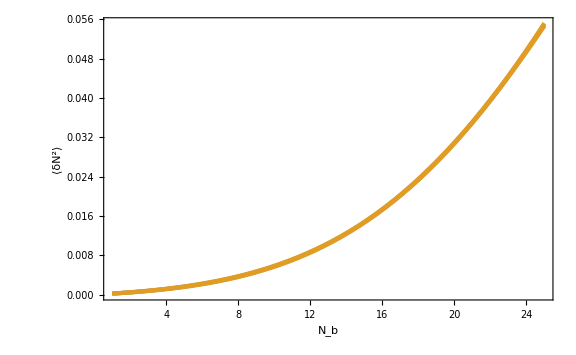

```mathematica
Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],"⟨δN^2⟩"}]
```

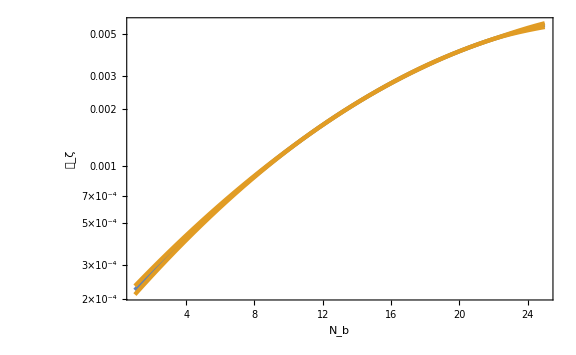

```mathematica
Show[LogPlot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],Subscript[𝒫, ζ]}],ListLogPlot[calPvsNb,PlotStyle->{Black,Dashed}]]
```

## Starobinsky

```mathematica
H0=10^-5;
V0=3 H0^2;
```

```mathematica
Ap=Sqrt[(9 H0^6)/(4 π^2 8.5 10^-10)];
Am=Ap/1700;
```

```mathematica
V[x_]:=V0+Ap x/;x>0
V[x_]:=V0+Am x/;x<=0
Vp[x_]:=Ap/;x>0
Vp[x_]:=Am/;x<=0
```

```mathematica
H[x_,p_]:=Sqrt[(p^2/2+V[x])/3];
```

```mathematica
xi=1.93 10^-2;
pi=-5.45 10^-7;
```

```mathematica
Hi=H[xi,pi];
tf=20/Hi;
```

```mathematica
sol=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+Vp[x[t]]==0,x[0]==xi,x'[0]==pi,NN'[t]==H[x[t],x'[t]],NN[0]==0},{x[t],x'[t],NN[t]},{t,0,tf}][[1]];
```

```mathematica
xsol[t_]=x[t]/.sol;
Nsol[t_]=NN[t]/.sol;
```

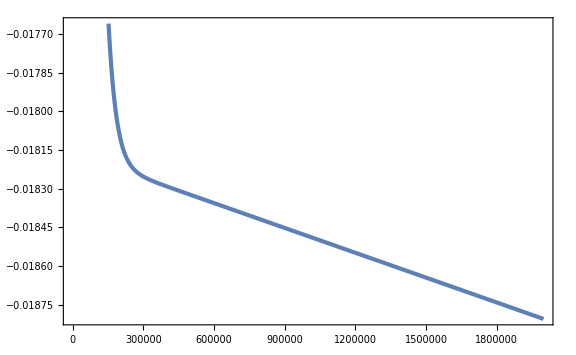

```mathematica
Plot[xsol[t],{t,0,tf}]
```

```mathematica
tend=t/.FindRoot[xsol[t]==-1.87 10^-2,{t,tf}]
```

1.66988×10^6

```mathematica
Nend=Nsol[tend]
```

16.699

```mathematica
MS=Import["calPlin_Starobinsky.csv"];
```

```mathematica
calPvsNb=Map[{Nend-Log[#[[1]]],#[[2]]}&,MS];
```

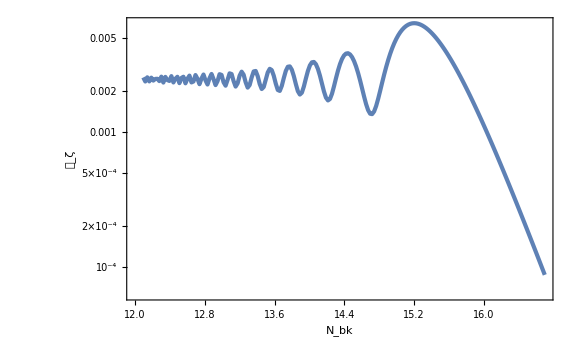

```mathematica
ListLogPlot[calPvsNb,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, "bk"],"Starobinsky"}}]
```

```mathematica
MiyamotoData=Import["NTot_Starobinsky_RandomNbk_1e6path.csv"];//AbsoluteTiming
```

{2.59261,Null}

```mathematica
Max[Drop[MiyamotoData,1][[All,1]]]
```

7.

#### 1e6

```mathematica
sample=10^6;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
Nbmin=Min[dN2vsNb[[All,1]]]
Nmax=Max[dN2vsNb[[All,1]]]
```

1.00001

7.

```mathematica
fit=NonlinearModelFit[dN2vsNb,f[x],{a,b,c},x]
```

b        -b + x
FittedModel[<|Type -> Nonlinear, Model -> <|FittedParameterRules -> {a -> 0.0260809, b -> 8.50992, c -> 9.01754}, IndependentVariables -> {x}, FitExpression -> a (Erf[-] + Erf[------]), ParameterConstraints -> True|>, Weights -> <|ExampleWeights -> 1|>, InputData -> {«1000000»}, Localizer -> Function[Null, Internal`LocalizedBlock[{a, b, c, x}, #1], {HoldAll}], Options -> {}|>]
                                                                                                                                                                       c          c

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.0260809 (0.817994+Erf[0.110895 (-8.50992+x)])

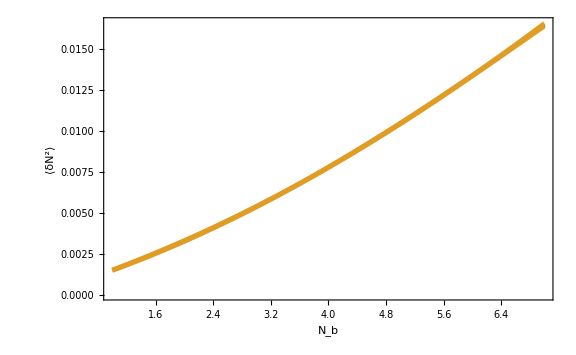

```mathematica
Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],"⟨δN^2⟩"}]
```

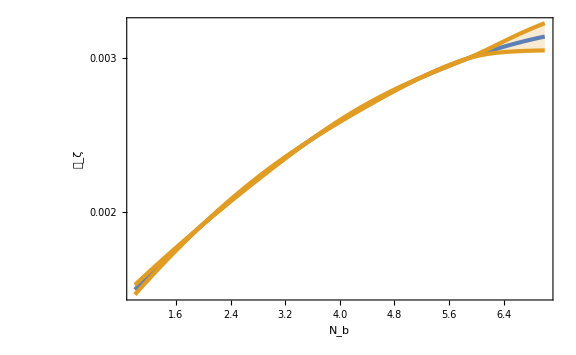

```mathematica
Show[LogPlot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],Subscript[𝒫, ζ]}],ListLogPlot[calPvsNb,PlotStyle->{Black,Dashed}]]
```

## Hybrid

```mathematica
MiyamotoData=Import["NTot_2pathsFromRandomNbk_1e7path.csv"];//AbsoluteTiming
```

{66.0227,Null}

### non-binning

#### 1e4

```mathematica
sample=10^4;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
Nbmin=Min[dN2vsNb[[All,1]]]
Nmax=Max[dN2vsNb[[All,1]]]
```

1.00079

29.9984

```mathematica
fit=NonlinearModelFit[dN2vsNb,f[x],{a,b,c},x]
```

FittedModel[…]

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.363225 (1.+Erf[0.364863 (-16.867+x)])

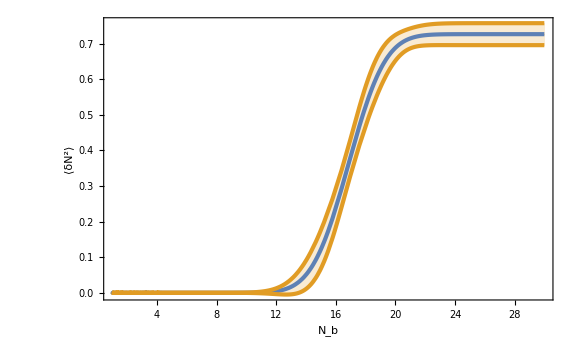

```mathematica
Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],"⟨δN^2⟩"}]
```

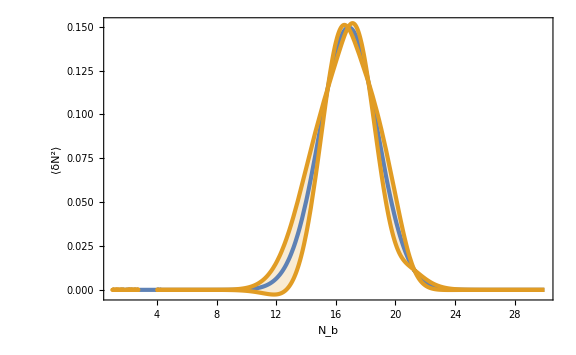

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],"⟨δN^2⟩"}]
```

#### 1e5

```mathematica
sample=10^5;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
Nbmin=Min[dN2vsNb[[All,1]]]
Nmax=Max[dN2vsNb[[All,1]]]
```

1.00004

29.9999

```mathematica
fit=NonlinearModelFit[dN2vsNb,f[x],{a,b,c},x]
```

b        -b + x
FittedModel[<|Type -> Nonlinear, Model -> <|FittedParameterRules -> {a -> 0.383979, b -> 16.9691, c -> 2.96484}, IndependentVariables -> {x}, FitExpression -> a (Erf[-] + Erf[------]), ParameterConstraints -> True|>, Weights -> <|ExampleWeights -> 1|>, InputData -> {«100000»}, Localizer -> Function[Null, Internal`LocalizedBlock[{a, b, c, x}, #1], {HoldAll}], Options -> {}|>]
                                                                                                                                                                      c          c

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.383979 (1.+Erf[0.337286 (-16.9691+x)])

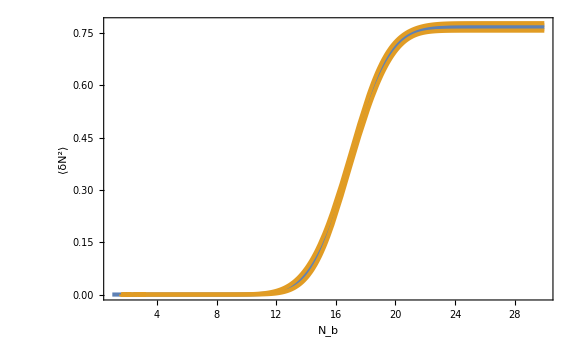

```mathematica
Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],"⟨δN^2⟩"}]
```

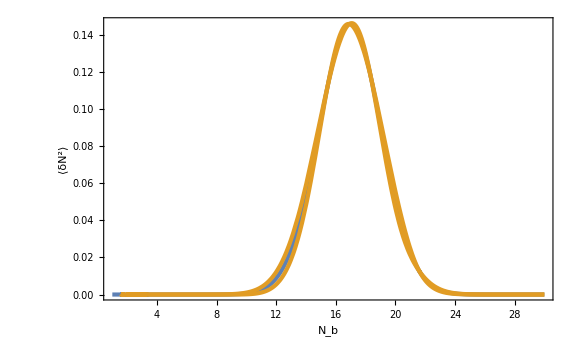

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],"⟨δN^2⟩"}]
```

#### 1e6

```mathematica
sample=10^6;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
Nbmin=Min[dN2vsNb[[All,1]]]
Nmax=Max[dN2vsNb[[All,1]]]
```

1.00001

30.

```mathematica
fit=NonlinearModelFit[dN2vsNb,f[x],{a,b,c},x]
```

b        -b + x
FittedModel[<|Type -> Nonlinear, Model -> <|FittedParameterRules -> {a -> 0.379298, b -> 16.9829, c -> 2.93259}, IndependentVariables -> {x}, FitExpression -> a (Erf[-] + Erf[------]), ParameterConstraints -> True|>, Weights -> <|ExampleWeights -> 1|>, InputData -> {«1000000»}, Localizer -> Function[Null, Internal`LocalizedBlock[{a, b, c, x}, #1], {HoldAll}], Options -> {}|>]
                                                                                                                                                                      c          c

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.379298 (1.+Erf[0.340996 (-16.9829+x)])

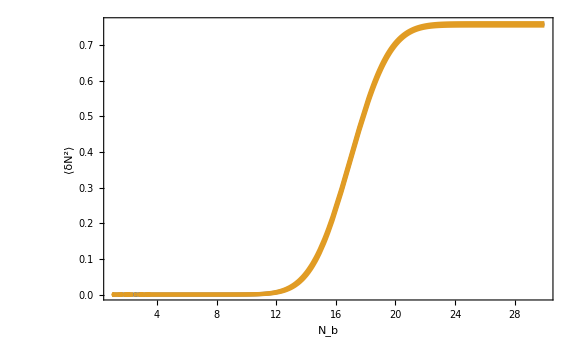

```mathematica
Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],"⟨δN^2⟩"}]
```

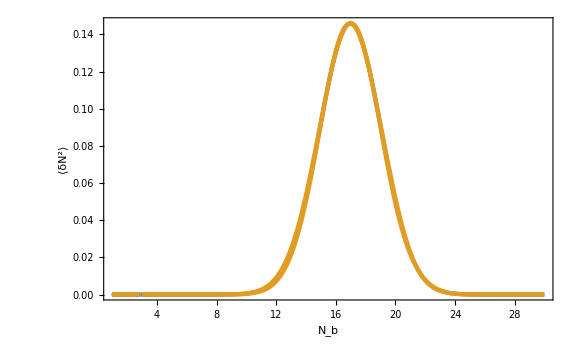

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],"⟨δN^2⟩"}]
```

#### 1e7

```mathematica
sample=10^7;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
Nbmin=Min[dN2vsNb[[All,1]]]
Nmax=Max[dN2vsNb[[All,1]]]
```

1.

30.

```mathematica
fit=NonlinearModelFit[dN2vsNb,f[x],{a,b,c},x]
```

b        -b + x
FittedModel[<|Type -> Nonlinear, Model -> <|FittedParameterRules -> {a -> 0.379228, b -> 16.9822, c -> 2.95285}, IndependentVariables -> {x}, FitExpression -> a (Erf[-] + Erf[------]), ParameterConstraints -> True|>, Weights -> <|ExampleWeights -> 1|>, InputData -> {«10000000»}, Localizer -> Function[Null, Internal`LocalizedBlock[{a, b, c, x}, #1], {HoldAll}], Options -> {}|>]
                                                                                                                                                                      c          c

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.379228 (1.+Erf[0.338655 (-16.9822+x)])

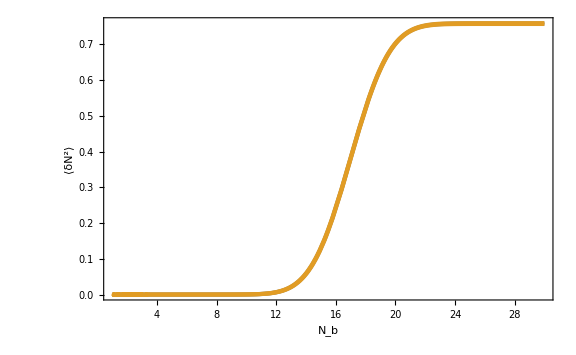

```mathematica
Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],"⟨δN^2⟩"}]
```

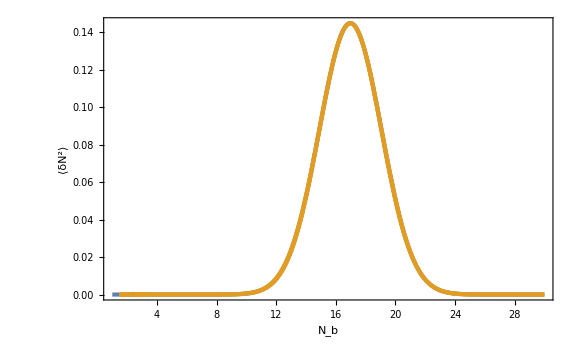

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],"⟨δN^2⟩"}]
```

### binning

```mathematica
err=10^-4;
sample=10^4;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
Length[dN2vsNb]
```

10000

```mathematica
NbList=dN2vsNb[[All,1]];
```

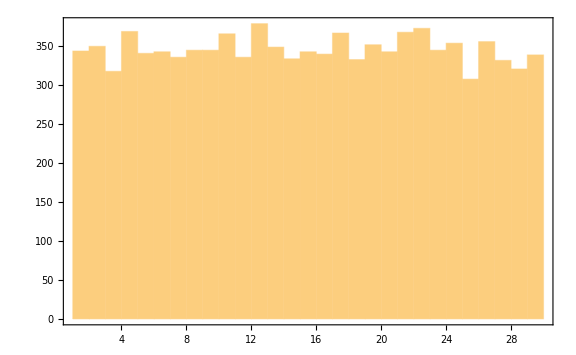

```mathematica
Histogram[NbList]
```

```mathematica
dN=1;
Nbmin=2;
Nmax=29;
```

```mathematica
binning[Nb_]:=Select[dN2vsNb,Nb-dN/2<=#[[1]]<Nb+dN/2&];
```

```mathematica
dN2List=ParallelTable[bindata=binning[Nb];
{Nb,If[Length[bindata]>1,Mean[bindata[[All,2]]]±Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err],0]},{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{0.198073,Null}

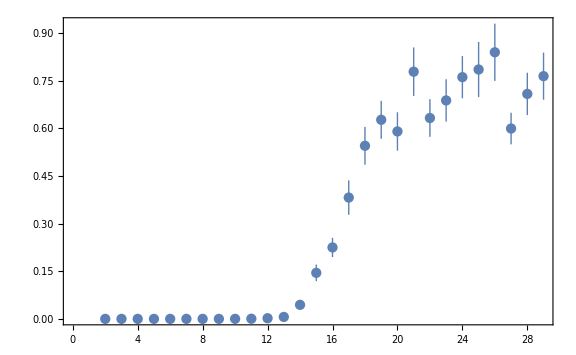

```mathematica
ListPlot[dN2List,Joined->False]
```

```mathematica
dN2we=ParallelTable[bindata=binning[Nb];
If[Length[bindata]>1,{Nb,Mean[bindata[[All,2]]],Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err]},None],{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{0.090569,Null}

```mathematica
weights=1/dN2we[[All,3]]^2;
```

```mathematica
Integrate[Exp[a0 LegendreP[0,x]+a1 LegendreP[1,x]-a2 LegendreP[2,x]],x]
```

(ⅇ^(a0+a1^2/(6 a2)+a2/2) √(π/6) Erf[(-a1+3 a2 x)/(√6 √a2)])/(√a2)

```mathematica
f[x_]=c/(1+Exp[-a0 LegendreP[0,x]-a1 LegendreP[1,x](*-a2 LegendreP[2,x]-a3 LegendreP[3,x]-a4 LegendreP[4,x]-a5 LegendreP[5,x]*)]);
g[x_]=a0 LegendreP[0,x]+a1 LegendreP[1,x]+a2 LegendreP[2,x]+a3 LegendreP[3,x]+a4 LegendreP[4,x]+a5 LegendreP[5,x];
h[x_]=a0 (Erf[a1(x-a2)]+a3);
```

```mathematica
fit=NonlinearModelFit[dN2we[[All,{1,2}]],(*f[x]*)(*g[x]*)h[x],{a0,a1,a2,a3(*,a4,a5*)(*,c*)},x,Weights->weights,MaxIterations->100000]
```

FittedModel[0.350062 (1.00012+Erf[0.409478 (-16.9263+x)])]

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.350062 (1.00012+Erf[0.409478 (-16.9263+x)])

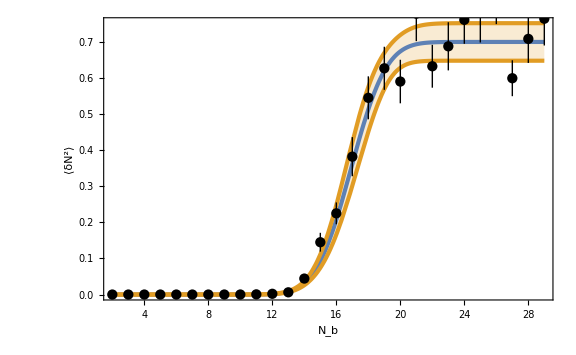

```mathematica
Show[Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],"⟨δN^2⟩"}],ListPlot[dN2List,Joined->False,PlotStyle->Black]]
```

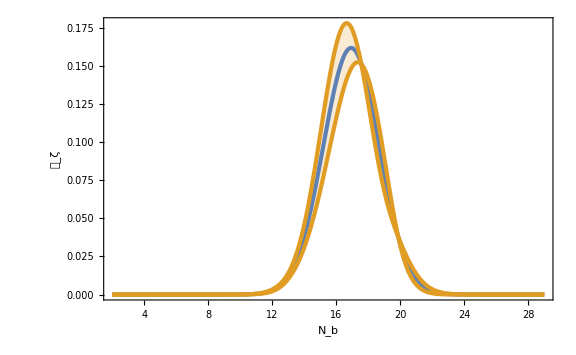

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},PlotRange->Full,Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],Subscript[𝒫, ζ]}]
```

#### N = 1e4

```mathematica
sample=10^4;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
binning[Nb_]:=Select[dN2vsNb,Nb-dN/2<=#[[1]]<Nb+dN/2&];
```

```mathematica
dN2List=ParallelTable[bindata=binning[Nb];
{Nb,If[Length[bindata]>1,Mean[bindata[[All,2]]]±Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err],0]},{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{0.173284,Null}

```mathematica
ListPlot[dN2List,Joined->False]
```

-Graphics-

```mathematica
dN2we=ParallelTable[bindata=binning[Nb];
If[Length[bindata]>1,{Nb,Mean[bindata[[All,2]]],Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err]},None],{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{0.08617,Null}

```mathematica
weights=1/dN2we[[All,3]]^2;
```

```mathematica
h[x_]=a0 (Erf[a1(x-a2)]+a3);
```

```mathematica
fit=NonlinearModelFit[dN2we[[All,{1,2}]],(*f[x]*)(*g[x]*)h[x],{a0,a1,a2,a3(*,a4,a5*)(*,c*)},x,Weights->weights,MaxIterations->100000]
```

FittedModel[0.350062 (1.00012+Erf[0.409478 (-16.9263+x)])]

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.350062 (1.00012+Erf[0.409478 (-16.9263+x)])

```mathematica
Show[Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{{"⟨δN^2⟩",None},{Subscript[N, "b"],𝒩==sample}}],ListPlot[dN2List,Joined->False,PlotStyle->Black]]
```

-Graphics-

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},PlotRange->Full,Filling->{2->{1}},FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, "b"],𝒩==sample}}]
```

-Graphics-

#### N = 1e5

```mathematica
sample=10^5;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
binning[Nb_]:=Select[dN2vsNb,Nb-dN/2<=#[[1]]<Nb+dN/2&];
```

```mathematica
dN2List=ParallelTable[bindata=binning[Nb];
{Nb,If[Length[bindata]>1,Mean[bindata[[All,2]]]±Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err],0]},{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{0.699842,Null}

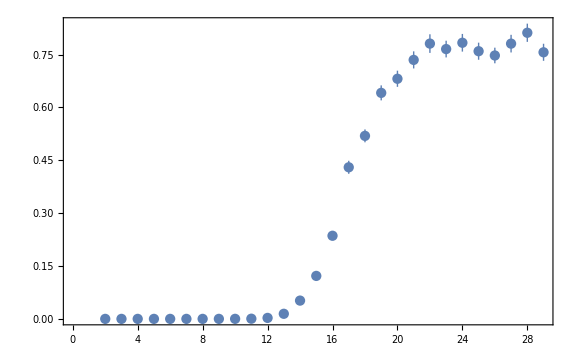

```mathematica
ListPlot[dN2List,Joined->False]
```

```mathematica
dN2we=ParallelTable[bindata=binning[Nb];
If[Length[bindata]>1,{Nb,Mean[bindata[[All,2]]],Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err]},None],{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{0.774621,Null}

```mathematica
weights=1/dN2we[[All,3]]^2;
```

```mathematica
h[x_]=a0 (Erf[a1(x-a2)]+a3);
```

```mathematica
fit=NonlinearModelFit[dN2we[[All,{1,2}]],(*f[x]*)(*g[x]*)h[x],{a0,a1,a2,a3(*,a4,a5*)(*,c*)},x,Weights->weights,MaxIterations->100000]
```

FittedModel[0.380373 (0.999992+Erf[0.38106 (-16.8998+x)])]

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.380373 (0.999992+Erf[0.38106 (-16.8998+x)])

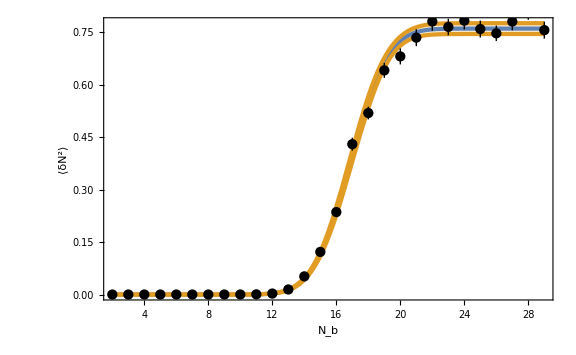

```mathematica
Show[Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{{"⟨δN^2⟩",None},{Subscript[N, "b"],𝒩==sample}}],ListPlot[dN2List,Joined->False,PlotStyle->Black]]
```

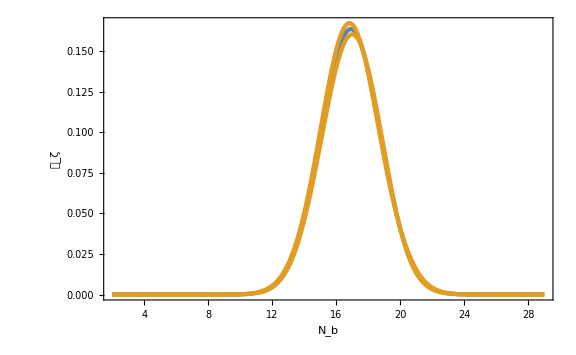

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},PlotRange->Full,Filling->{2->{1}},FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, "b"],𝒩==sample}}]
```

#### N = 1e6

```mathematica
sample=10^6;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
binning[Nb_]:=Select[dN2vsNb,Nb-dN/2<=#[[1]]<Nb+dN/2&];
```

```mathematica
dN2List=ParallelTable[bindata=binning[Nb];
{Nb,If[Length[bindata]>1,Mean[bindata[[All,2]]]±Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err],0]},{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{5.54572,Null}

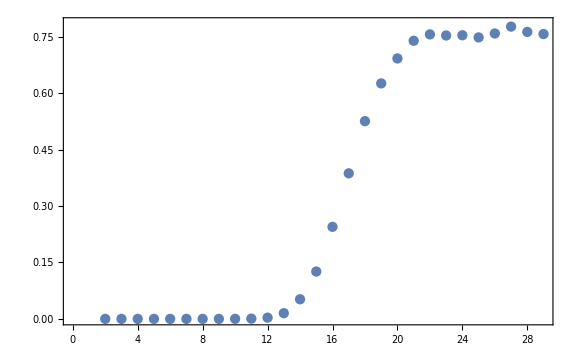

```mathematica
ListPlot[dN2List,Joined->False]
```

```mathematica
dN2we=ParallelTable[bindata=binning[Nb];
If[Length[bindata]>1,{Nb,Mean[bindata[[All,2]]],Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err]},None],{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{5.52411,Null}

```mathematica
weights=1/dN2we[[All,3]]^2;
```

```mathematica
h[x_]=a0 (Erf[a1(x-a2)]+a3);
```

```mathematica
fit=NonlinearModelFit[dN2we[[All,{1,2}]],(*f[x]*)(*g[x]*)h[x],{a0,a1,a2,a3(*,a4,a5*)(*,c*)},x,Weights->weights,MaxIterations->100000]
```

FittedModel[0.377094 (0.999939+Erf[0.366619 (-16.9312+x)])]

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.377094 (0.999939+Erf[0.366619 (-16.9312+x)])

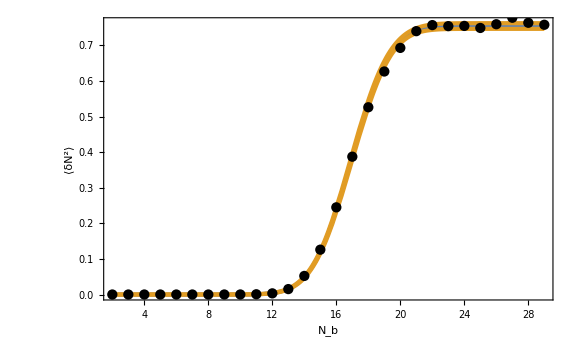

```mathematica
Show[Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{{"⟨δN^2⟩",None},{Subscript[N, "b"],𝒩==sample}}],ListPlot[dN2List,Joined->False,PlotStyle->Black]]
```

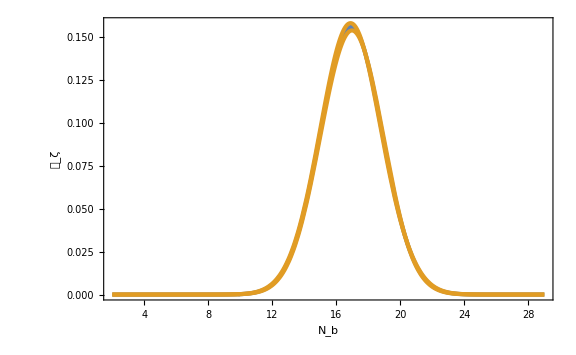

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},PlotRange->Full,Filling->{2->{1}},FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, "b"],𝒩==sample}}]
```

#### N = 1e7

```mathematica
sample=10^7;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
binning[Nb_]:=Select[dN2vsNb,Nb-dN/2<=#[[1]]<Nb+dN/2&];
```

```mathematica
dN2List=ParallelTable[bindata=binning[Nb];
{Nb,If[Length[bindata]>1,Mean[bindata[[All,2]]]±Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err],0]},{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{57.1784,Null}

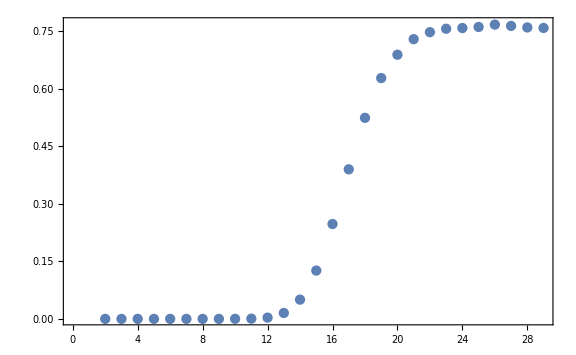

```mathematica
ListPlot[dN2List,Joined->False]
```

```mathematica
dN2we=ParallelTable[bindata=binning[Nb];
If[Length[bindata]>1,{Nb,Mean[bindata[[All,2]]],Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err]},None],{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{59.8831,Null}

```mathematica
weights=1/dN2we[[All,3]]^2;
```

```mathematica
h[x_]=a0 (Erf[a1(x-a2)]+a3);
```

```mathematica
fit=NonlinearModelFit[dN2we[[All,{1,2}]],(*f[x]*)(*g[x]*)h[x],{a0,a1,a2,a3(*,a4,a5*)(*,c*)},x,Weights->weights,MaxIterations->100000]
```

FittedModel[0.376939 (0.999692+Erf[0.363006 (-16.9355+x)])]

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.376939 (0.999692+Erf[0.363006 (-16.9355+x)])

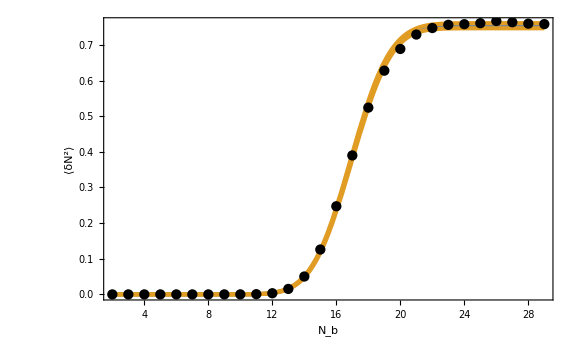

```mathematica
Show[Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{{"⟨δN^2⟩",None},{Subscript[N, "b"],𝒩==sample}}],ListPlot[dN2List,Joined->False,PlotStyle->Black]]
```

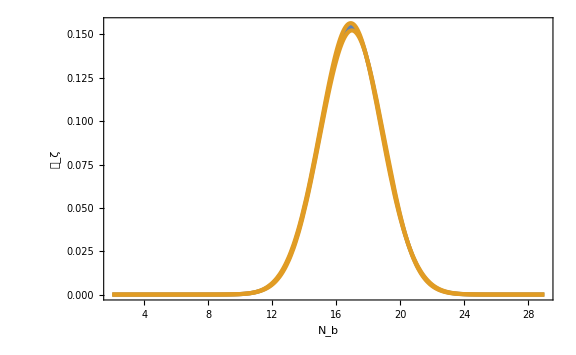

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},PlotRange->Full,Filling->{2->{1}},FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, "b"],𝒩==sample}}]
```